```mathematica
e2[n_,k_]:=e2[n,k]=Sum[e2[j,k-1] e2[n/j,1],{j,Divisors[n]}];e2[n_,1]:=(-1)^(n+1);e2[1,1]:=0;e2[n_,0]:=0;e2[1,0]:=1
E2[n_,k_] := E2[n,k]=Sum[ e2[j,k],{j,2,n}]
l2[n_]:=l2[n]=Sum[(-1)^(k+1)/k e2[n,k],{k,1,Log[2,n]}]
L2[n_]:=L2[n]=Sum[(-1)^(k+1)/k E2[n,k],{k,1,Log[2,n]}]
P2[n_, 0]:=1
P2[n_, k_]:= P2[n,k] = Sum[ l2[j] P2[Floor[n/j],k-1],{j,2,n}]
Ex2[n_, z_] := Sum[ z^k / (k!) P2[n,k],{k,0,Log[2,n]}]
```

```mathematica
P2[100,2]
```

-419/36

```mathematica
L2[100]
```

4/5

```mathematica
Ex2[100,-I]
```

371/72+(109 ⅈ)/24

```mathematica
Animate[DiscretePlot[ Ex2[n,ss]/ss,{n,2,100}],{ss,-2,2}]
```

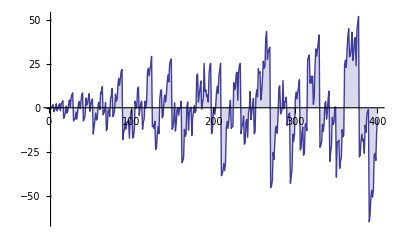

```mathematica
DiscretePlot[ Ex2[n,ss=4]/ss,{n,2,400}]
```

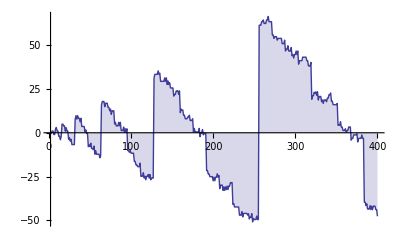

```mathematica
DiscretePlot[ P2[n,2],{n,2,400}]
```

```mathematica
P2[100,1]
```

4/5

```mathematica
E2[100,2]
```

3

```mathematica
Sum[ (-1)^( k-j), {j,2,100},{k,2,Floor[100/j]}]
```

3

```mathematica
Expand[E2[n,1]]
```

-1/2-(-1)^n/2

```mathematica
E2[x,2]
```

0

```mathematica
E2[14,2]
```

-2

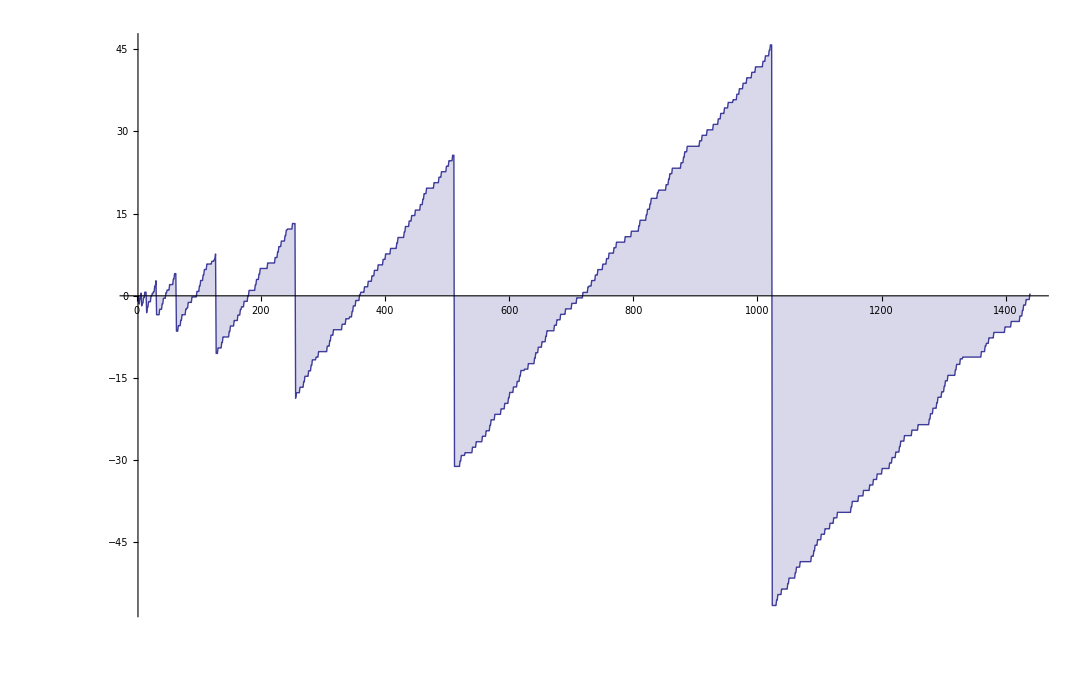

```mathematica
P2[n_,k_] := P2[n,k]=Sum[ (-1)^(j+1)( 1/k - P2[Floor[n/j],k+1]), {j,2,n}]
DiscretePlot[ P2[n,1],{n,2,90*16}]
```

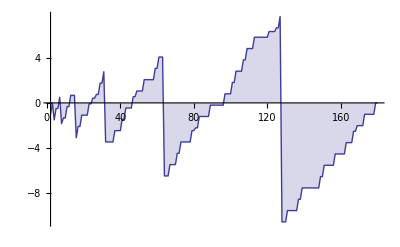

```mathematica
P2a[n_,k_] := Sum[ (-1)^(j+1)( 1/k ), {j,2,n}]+Sum[ (-1)^(j+1)( - P2a[n/j,k+1]), {j,2,n}]
DiscretePlot[ P2a[n,1],{n,2,90*2}]
```

```mathematica
Expand[Sum[ (-1)^(j+1)( 1/k ), {j,2,n}]]
```

-1/(2 k)-(-1)^n/(2 k)

```mathematica
P2a[n_, k_] :=Sum[ (-1)^(j+1), {j,2,n}]/k+Sum[ (-1)^(j+1)( - P2a[n/j,k+1]), {j,2,n}]
DiscretePlot[ P2a[n,1],{n,2,90*2}]
```

-Graphics-

```mathematica
Sum[ (-1)^(j+1), {j,2,n}]
```

1/2 (-1-(-1)^n)

```mathematica
P2a[n_, k_] :=-(1/2 (1+(-1)^n))/k+Sum[ (-1)^j( P2a[Floor[n/j],k+1]), {j,2,n}]
DiscretePlot[ P2a[n,1],{n,2,90*2}]
```

-Graphics-